This notebook models propagation of Gaussian beams and allows one to figure out how inserting different beam-shaping optics affects their propagation.

## Definitions

First, the initial beam size is defined in terms of the x and y (wzerovert and wzerohoriz) and beam waist locations (zzerovert and zzerohoriz); z is the direction of propagation of the beam.
- λ is the wavelength of the light;
- "inversezero" represents the complex beam parameter;

```mathematica
wzerovert=995*10^-6 ;
zzerovert=-21.4*10^(-2);
wzerohoriz= 800*10^-6;
zzerohoriz=200*10^(-2);
λ=922*10^-9;
inversezerohoriz=(-ⅈ λ)/(π wzerohoriz^2);
inversezerovert=(-ⅈ λ)/(π wzerovert^2);

freespace[z_,inverse_]:=inverse/(1+z*inverse);
waist[λ_, inverse_]:=√(-λ/(π Im[inverse]));
lens[f_,inverse_]:=-1/f+inverse;
```

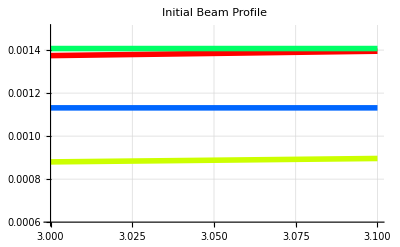

```mathematica
Plot[{waist[λ,freespace[(z-zzerovert),inversezerovert]],waist[λ,freespace[(z-zzerohoriz),inversezerohoriz]],wzerovert*Sqrt[2],wzerohoriz*Sqrt[2]},{z,300*10^(-2),310*10^-2},
PlotStyle->{{Hue[0],Thickness[.01]},{Hue[0.2],Thickness[.01]},{Hue[0.4],Thickness[.01]},{Hue[0.6],Thickness[.01]}},PlotLabel->"Initial Beam Profile", PlotRange->{0.6*10^(-3),1.5*10^-3},GridLines->Automatic ] (*Plotted 1/e^2 waists and Rayleigh range of 1/e^2 waists*) (*,wzerovert*Sqrt[2],wzerohoriz*Sqrt[2]*)
```

```mathematica
zlensvert1=13.5*10^(-2);
flensvert1=80*10^(-3);
Plot[{waist[λ,freespace[(z-zzerovert),inversezerovert]],waist[λ,freespace[(z-zzerohoriz),inversezerohoriz]],waist[λ,freespace[(z-zlensvert1),lens[flensvert1,freespace[(zlensvert1-zzerovert),inversezerovert]]]]},{z,-.5,4},
PlotLabel->"V 1/e^2 waist after 80mm lens",PlotStyle->{{Hue[0],Thickness[.01]},{Hue[0.2],Thickness[.01]},{Hue[0.4],Thickness[.01]},{Hue[0.6],Thickness[.01]}}, PlotRange->{.5*10^(-3),1.5*10^(-3)},GridLines->Automatic ]
```

General::spell1: Possible spelling error: new symbol name "flensvert1" is similar to existing symbol "zlensvert1". More…

⁃Graphics⁃

```mathematica
zlensvert1=13.5*10^(-2);
flensvert1=80*10^(-3);
zlensvert2=.2966
flensvert2=80*10^(-3);

Plot[{waist[λ,freespace[(z-zzerovert),inversezerovert]],waist[λ,freespace[(z-zzerohoriz),inversezerohoriz]],waist[λ,freespace[(z-zlensvert1),lens[flensvert1,freespace[(zlensvert1-zzerovert),inversezerovert]]]],waist[λ,freespace[(z-zlensvert2),lens[flensvert2,freespace[(zlensvert2-zlensvert1),lens[flensvert1,freespace[(zlensvert1-zzerovert),inversezerovert]]]]]]},{z,0,2.5},PlotLabel->"V 1/e^2 waist after two 80mm lens",
PlotStyle->{{Hue[0],Thickness[.01]},{Hue[0.2],Thickness[.01]},{Hue[0.4],Thickness[.01]},{Hue[0.6],Thickness[.01]}}, PlotRange->{0*10^(-3),1.2*10^(-3)},GridLines->Automatic ]
```

0.2966

General::spell1: Possible spelling error: new symbol name "flensvert2" is similar to existing symbol "zlensvert2". More…

⁃Graphics⁃

```mathematica
PFL= 11.14*10^(-3);(*Pigtail focal length*)   PNA=7.2*10^(-3)/(2*11*10^(-3));(*Pigtail Numerical Aperture*)
wzerovert=N[1*10^(-3)];   (*ASSUMING THAT THE WAIST OF THE FIBER IS AT THE PIGTAIL OUTPUT; FOR A 2 MM 1/e^2 DIA.*)
zzerovert=0; wzerohoriz=wzerovert; zzerohoriz=0;
inversezerohoriz=(-ⅈ λ)/(π wzerohoriz^2);  inversezerovert=(-ⅈ λ)/(π wzerovert^2);
zlensvert1=.02; flensvert1=300*10^(-3);
flensvert2=.75;
zlensvert2=zlensvert1+flensvert1+flensvert2+0.0;  (*CAUSING A ONE-TO-ONE TELESCOPE WITH f=300 MM LENSES*)  (*300*10^(-3);*)
zlensvert3=1.55;  flensvert3=177.213*10^(-3);  (*focusing lens is ~1.55 meters from the first telescoping lens*)

Plot[{4*waist[λ,freespace[(z-zzerovert),inversezerovert]],4*wzerovert*Sqrt[2]},
{z,0,3},
PlotLabel->"V 1/e^4 beam diameter out of fiber",PlotStyle->{{Dashing[{0.1,0.07}],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[0,0,1]}}, PlotRange->{0*10^(-3),10*10^(-3)},GridLines->Automatic ];

spotsize[z_,λ_,w_]:=w*√(1+((λ z)/(π w^2))^2);
Waist50umviewport=4*spotsize[viewport,922*10^(-9),50*10^(-6)];  (*size of beam with w0=50um at 1/e^4 intensity in meters, 4.82" away from w0*)

Waist50umflensunknown=4*spotsize[6.89*2.54/100,922*10^(-9),50*10^(-6)];     (*size of beam with w0=50um at 1/e^4 intensity in meters, 6.89" away from w0; for f=175mm lens*)

Plot[{4*waist[λ,freespace[(z-zzerovert),inversezerovert]],
4*waist[λ,freespace[(z-zlensvert1),lens[flensvert1,freespace[(zlensvert1-zzerovert),inversezerovert]]]],4*waist[λ,freespace[(z-zlensvert2),lens[flensvert2,freespace[(zlensvert2-zlensvert1),lens[flensvert1,freespace[(zlensvert1-zzerovert),inversezerovert]]]]]],4*waist[λ,freespace[(z-zlensvert3),lens[flensvert3,freespace[(zlensvert3-zlensvert2),lens[flensvert2,freespace[(zlensvert2-zlensvert1),lens[flensvert1,freespace[(zlensvert1-zzerovert),inversezerovert]]]]]]]],
4*0.05*10^(-3),Waist50umflensunknown},
{z,0,zlensvert3+2*flensvert3},
PlotLabel->"V 1/e^4 beam diameter after fiber, telescoping lenses, and focusing lens to chamber",PlotStyle->{{Dashing[{0.1,0.09}],RGBColor[0,0,1]},{Dashing[{0.15,0.02}],RGBColor[0,0,1]},{Thickness[0.001],RGBColor[0,0,1]},{Thickness[0.001],RGBColor[1,0,0]},{Thickness[0.002],RGBColor[0,1,0]},{Thickness[0.01],RGBColor[0,1,0]}}, PlotRange->{0*10^(-3),11*10^(-3)},GridLines->Automatic ];
```

```mathematica
w=1.25
Plot[Exp[-2*r^2/(w^2 )],{r,-3,3}]
w=1.4
Plot[Exp[-2*r^2/(w^2 )],{r,-3,3}]
```

1.25

⁃Graphics⁃

1.4

⁃Graphics⁃

```mathematica
viewport
```

0.122428

```mathematica
Solve[ArcTan[N[(x/68)]]*(180/(Pi))==5,x]
```

{{x→5.94923}}

```mathematica
11.25-5.95
```

5.3